# QSP / QSVT Unification — Interactive Notebook

Executable companion to the QSP/QSVT pipeline reproducing the core constructions of Martyn, Rossi, Tan & Chuang, "Grand Unification of Quantum Algorithms" (PRX Quantum 2, 040203, 2021) and the QSP Hamiltonian-simulation construction of Low & Chuang, "Optimal Hamiltonian Simulation by Quantum Signal Processing" (PRL 118, 010501, 2017). Outputs shown here were generated by make_notebook.wls; re-evaluate any cell to reproduce. Convention (Wx): W(a)=e^{i arccos(a) X}, S(ϕ)=e^{i ϕ Z}, P(a)=⟨0|U|0⟩.

## Setup — load the package

Loads the reusable package from this notebook's own folder.

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{NotebookDirectory[], "src", "QSPUnification.wl"}]];
```

## Demo 1 — QSP ⟹ Chebyshev polynomials

Symbolic derivation: zero-phase QSP of degree d yields P = T_d and Q = U_{d-1}, satisfying the Pell/Chebyshev identity T_d^2+(1-a^2)U_{d-1}^2=1.

```mathematica
Dataset[Table[ChebyshevDerivation[d], {d, 1, 6}]]
```

Numerical check at a=0.6, d=5: Re P_5(0.6) equals T_5(0.6).

```mathematica
d1 = 5;
phases0 = ConstantArray[0., d1 + 1];
u = QSPUnitary[phases0, 0.6];
{Re[u[[1, 1]]], ChebyshevT[d1, 0.6]}
```

{-0.07584,-0.07584}

The zero-phase QSP response traces the Chebyshev polynomial exactly.

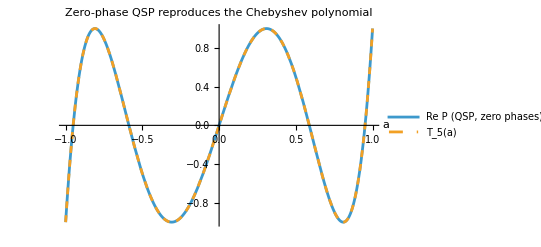

```mathematica
Plot[{QSPRealResponse[ConstantArray[0., 6], a], ChebyshevT[5, a]}, {a, -1, 1},
 PlotLegends -> {"Re P (QSP, zero phases)", "T_5(a)"},
 PlotStyle -> {Thick, Dashed}, AxesLabel -> {"a", ""},
 PlotLabel -> "Zero-phase QSP reproduces the Chebyshev polynomial"]
```

## Demo 2 — Hamiltonian simulation e^{-iHt}

Jacobi–Anger expansion approximates cos(t a) and sin(t a) by polynomials whose coefficients are Bessel functions (t=2, K=6).

```mathematica
cosData = JacobiAngerCos[2.0, 6];
sinData = JacobiAngerSin[2.0, 6];
{"cos degree" -> cosData["Degree"], "sin degree" -> sinData["Degree"]}
```

{cos degree→12,sin degree→13}

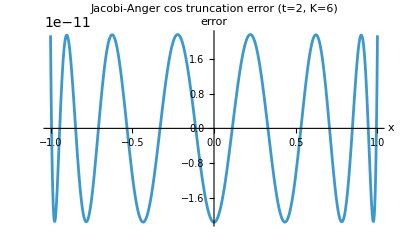

```mathematica
Plot[cosData["Function"][x] - Cos[2.0 x], {x, -1, 1},
 PlotLabel -> "Jacobi-Anger cos truncation error (t=2, K=6)",
 AxesLabel -> {"x", "error"}]
```

Build a driven truncated-Fock Hamiltonian from the Quantum Framework's second-quantization operators, normalized so the spectral norm is ≤ 1.

```mathematica
H = BuildHamiltonian[];
Column[{
  "dimension: " <> ToString[H["Dimension"]],
  "eigenvalues: " <> ToString[H["Eigenvalues"]],
  "spectral norm: " <> ToString[Max[Abs[H["Eigenvalues"]]]]}]
```

dimension: 4
eigenvalues: {-0.705992, -0.310659, 0.166651, 0.85}
spectral norm: 0.85

Generate symmetric QSP phase angles so Re P approximates the (scaled) cos and sin targets.

```mathematica
eta = 0.1; t = 2.0;
cosPh = FindQSPPhases[Function[x, (1 - eta) Cos[t x]], 12, "Restarts" -> 6];
sinPh = FindQSPPhases[Function[x, (1 - eta) Sin[t x]], 13, "Restarts" -> 6];
{"cos max error" -> cosPh["MaxError"], "sin max error" -> sinPh["MaxError"]}
```

{cos max error→2.78753×10^-7,sin max error→6.59942×10^-8}

Reconstruct e^{-iHt} from the QSP cos/sin responses and compare to the exact matrix exponential.

```mathematica
recon = ReconstructEvolution[H["Matrix"], t, cosPh["Phases"], sinPh["Phases"], eta];
{"max abs error" -> recon["MaxAbsError"], "overlap" -> recon["NormalizedOverlap"]}
```

{max abs error→1.34261×10^-7,overlap→1.}

## Full numerical validation suite

Runs the package's complete validation suite (same checks exported by build_project.wls).

```mathematica
Dataset[RunValidationSuite[]]
```

## References

[1] J. M. Martyn, Z. M. Rossi, A. K. Tan, I. L. Chuang, Grand Unification of Quantum Algorithms, PRX Quantum 2, 040203 (2021).
[2] G. H. Low, I. L. Chuang, Optimal Hamiltonian Simulation by Quantum Signal Processing, Phys. Rev. Lett. 118, 010501 (2017).